## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`';
Get["MASSef`"];
Get["MASSef`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
rxnName="dPGM";
fitLabel=rxnName;
dataFileName=rxnName;

(*KeqEquilibrator=5.3;*) (*The real value*)
KeqEquilibrator=0.7; (*The value that works with the kinetic data*)

assumedUncertaintyFraction = 0.05;
removeInputFiles = False;
removeOutputFiles = True;

(* user will need to change this path *)
pathMASSFittingPackage = "C:/MASSef/";

mainFolder = "fit_PGM";
{workingDir, pathData, runFitScriptPath, inputPath, outputPath, bigg2equilibrator}=initializeNotebook[pathMASSFittingPackage, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:C:\MASSef\examples\

## Import Data

```mathematica
enzymeDataPath = FileNameJoin[{pathData, "kinetic_data.csv"}, OperatingSystem->$OperatingSystem];
bufferInfoDataPath = FileNameJoin[{pathData, "buffer_info.csv"}, OperatingSystem->$OperatingSystem];
ionChargeDataPath = FileNameJoin[{pathData, "ion_charge.csv"}, OperatingSystem->$OperatingSystem];

{rxn, mechanism, structure, nActiveSites, nAllostericSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}=getEnzymeData[rxnName, enzymeDataPath, assumedUncertaintyFraction];

bufferInfo = getBufferInfoData[bufferInfoDataPath];
ionCharge = getIonData[ionChargeDataPath];

inhibitorMet={};
affectedMets={};(*There can be multiple metabolites*)
```

## Construct Module and Set Up Comparison Equations

### Print Module Dependent Information

```mathematica
printEnzymeData[rxn, mechanism, structure, nActiveSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((2pg)^c⇌(3pg)^c)^dPGM

Null;

Structure: 2

Active sites: 2

Km Values:

Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
3pg | 0.0002 | 0.00019
0.00021 |  | M | 7 | 30 | trishcl | 0.03 | k | 0.02
cl | 0.02
mg2 | 0.005
so4 | 0.005
2pg | 0.00019 | 0.0001805
0.0001995 |  | M | 7 | 30 | trishcl | 0.03 | k | 0.02
cl | 0.02
mg2 | 0.005
so4 | 0.005

S0.5 Values:

Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
3pg | Null | 330 | 313.5
346.5 | 1/s | 7 | 30 | trishcl | 0.03 | k | 0.02
cl | 0.02
mg2 | 0.005
so4 | 0.005
2pg | Null | 220 | 209.
231. | 1/s | 7 | 30 | trishcl | 0.03 | k | 0.02
cl | 0.02
mg2 | 0.005
so4 | 0.005

Inhibition Values:

Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Parameter_Type | Metabolite | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Construct enzyme module

```mathematica
Overscript[(2pg)^c⇌(3pg)^c, dPGM]
```

```mathematica
"no reported mechanism"
```

```mathematica
catalyticBranch={"E_dPGM[c] + 2pg[c] <=> E_dPGM[c]&2pg",
				"E_dPGM[c]&2pg <=> E_dPGM[c]&3pg",
				"E_dPGM[c]&3pg<=> E_dPGM[c] + 3pg[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
```

### Setup King-Altman Equations

```mathematica
{reverseZeroSub, forwardZeroSub, metSatForSub, metSatRevSub} = getMetsSub[rxn];
rates = getEnzymeRates[enzymeModel];
{KeqName, KeqVal, volumeSub} = getMisc[enzymeModel, rxnName];

(*competitiveRxns={};(*Initialization for later. Do not modify this*)
eqRateConstSub={};(*Initialization for later. Do not modify this*)*)

(*You could modify these, but you shouldn't unless you run into problems*)

lowerParamBound=-6;
upperParamBound=9;
simplifyMaxTime=1*^-5;

(*Extract Transition ID from Mass Action Equations and Separate Catalytic and Non-Catalytic Reactions*)
(*The transition indices are extracted based off of the sum of their mass action stoichiometry.Reactions with a sum of zero are assumed to be catalytic.*)

(*Separate Catalytic and Non-Catalytic Reactions*)
{allCatalyticReactions, nonCatalyticReactions}=classifyReactions[enzymeModel];


(*Identify Transition Rate Equations*)
transitionID =getTransitionIDs[allCatalyticReactions];

(*Extract Transition Rate Equations*)
transitionRateEqs=getTransitionRateEqs[transitionID, rates];

unifiedRateConstList=getUnifiedRateConstList[allCatalyticReactions, nonCatalyticReactions];


(* semi-automated add competitive inhibition steps - none in this enzyme*)
eqRateConstSub={};


(*King-Altman Workaround UsingMathematicaSolve*)
(*This section of code will check to see if there is a 'absoluteFlux.m' file in the notebook directory from a previous cell evalution, and it will either derive a generalized flux equation (may take a long time) or import the previously derived flux equation. Note: If you modify the binding mechanism used in the constructEnzymeModule or manually add additional reactions to the model, you should delete the 'absoluteFlux.m' file in this notebook's current directory.*)
simplifyMaxTime = 100; (*in seconds*)
absoluteFlux=getFluxEquation[inputPath, rxnName, enzymeModel, unifiedRateConstList, transitionRateEqs, simplifyMaxTime, nActiveSites];


(*Equivalent Rate Constant Substitution for Random Ordered Mechanisms*)
(*This should work automatically,a substitution rule list is created with the name:'eqRateConstSub'.It is kind of a greedy section of code,so double check the results to make sure they're accurate*)
eqRateConstSub=getEquivRateConsts[enzymeModel, eqRateConstSub, nonCatalyticReactions];

(*Assemble Kinetic MASS Action Comparision Equations that Match to Km and kcat Data*)
(*Simplify fixes Python evaluation issues dealing with fractional exponents (e.g.'(-1)**(3/5)' returns 1.0)*)
{absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse}=getRateEqs[absoluteFlux, unifiedRateConstList, eqRateConstSub, reverseZeroSub, forwardZeroSub, volumeSub, metSatForSub, metSatRevSub];

(*Assemble Rate Constant And Metabolite Substitutions for Export*)
{finalRateConsts,metsFull, metsSub, rateConstsSub}=getMetRatesSubs[enzymeModel, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse,KeqVal];

(*Export Equations*)
{eqnNameList, eqnValList, eqnValListPy, fileList, fileListSub}=exportRateEqs[inputPath, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, metsSub, metSatForSub, metSatRevSub, rateConstsSub];
```

## Semi-Automated Simulate Data

### User Input Section

```mathematica
logStepSize=0.2;
(*nonKmParamWeight=3;*)
(*Weighting factor for non-Km data points. You can be specify this manually*)
{minPsDataVal, maxPsDataVal}= getMinMaxPsDataVal[1];
nonKmParamWeight=Length[Table[1,{i,minPsDataVal, maxPsDataVal,logStepSize}]];
eTotal=1;(*Enzyme Total, Should Be 1 for Fitting*)
assumedSaturatingConc=0.01 ;(*in Molarity*)

(*Chemical Activity Correction Options*)
inVivoPH=7.5;(*Assumed in vivo pH*)
inVivoIS=0.25;(*Assumed in vivo Ionic Strength, in Molarity*)
effectiveIonDiameter=3;(*Used in Debye-Huckel equation, in Angstroms*)

(*Initialization of Chemical Activity Correction. These values represent no correction (i.e. Chemical Activity is just the Metabolite Concentration)*)
activeIsoSub=Thread[metsFull->metsFull];(*[S^z] = [S] *)
activityCoefficient=Thread[metsFull->1];(* γ = 1 *)
```

### Simulate data

```mathematica
pHandT={8.9, 22};

kmFittingData= simulateKmData[rxn, metsFull,  metSatForSub, metSatRevSub, kmList, otherParmsList, assumedSaturatingConc, eTotal,
			   logStepSize,activeIsoSub, bufferInfo, ionCharge, inputPath,  fileList, KeqEquilibrator];

kcatFittingData=simulateKcatData[rxn, metsFull,  metSatForSub, metSatRevSub, kcatList, otherParmsList, assumedSaturatingConc, eTotal,
			  logStepSize, nonKmParamWeight, activeIsoSub, bufferInfo, ionCharge, inputPath, 
			  fileList, KeqEquilibrator];


haldane=haldaneRelation[KeqName,allCatalyticReactions]/.unifiedRateConstList;
haldaneRatio=haldane[[2]];

{KeqFittingData, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy}=simulateRateConstRatiosData[haldaneRatio,KeqEquilibrator, KeqEquilibrator, metsFull, rateConstsSub, metsSub, eTotal, nonKmParamWeight, inputPath, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy, pHandT,"haldaneRatio"];
```

### Assemble and export All Data

```mathematica
header=Join[Map[ToString, metsSub[[All,1]]],{"FileFlag", "Target_Data"}];

fittingData = Flatten[{kmFittingData,kcatFittingData, KeqFittingData}, 1];

dataPath =FileNameJoin[{inputPath,rxnName <>".dat"}, OperatingSystem->$OperatingSystem];

vList=Join[{header},fittingData];
Export[dataPath,vList,"Table"];
FilePrint[dataPath]
```

Keq_dPGM	2pg[c]	3pg[c]	param_dPGM_total	param_pH	param_Temp	FileFlag	Target_Data
0.7	0	0.00002	1	7	30	"C:\MASSef\examples\fit_PGM\input\relRateRev_3pg.txt"	0.09090909090909091
0.7	0	0.00003169786384922229	1	7	30	"C:\MASSef\examples\fit_PGM\input\relRateRev_3pg.txt"	0.13680688860321008
0.7	0	0.00005023772863019165	1	7	30	"C:\MASSef\examples\fit_PGM\input\relRateRev_3pg.txt"	0.2007600089131019
0.7	0	0.00007962143411069939	1	7	30	"C:\MASSef\examples\fit_PGM\input\relRateRev_3pg.txt"	0.2847472489508013
0.7	0	0.0001261914688960386	1	7	30	"C:\MASSef\examples\fit_PGM\input\relRateRev_3pg.txt"	0.38686317984685686
0.7	0	0.00020000000000000004	1	7	30	"C:\MASSef\examples\fit_PGM\input\relRateRev_3pg.txt"	0.5
0.7	0	0.0003169786384922229	1	7	30	"C:\MASSef\examples\fit_PGM\input\relRateRev_3pg.txt"	0.6131368201531432
0.7	0	0.0005023772863019165	1	7	30	"C:\MASSef\examples\fit_PGM\input\relRateRev_3pg.txt"	0.7152527510491988
0.7	0	0.0007962143411069948	1	7	30	"C:\MASSef\examples\fit_PGM\input\relRateRev_3pg.txt"	0.7992399910868982
0.7	0	0.0012619146889603862	1	7	30	"C:\MASSef\examples\fit_PGM\input\relRateRev_3pg.txt"	0.8631931113967899
0.7	0	0.0020000000000000005	1	7	30	"C:\MASSef\examples\fit_PGM\input\relRateRev_3pg.txt"	0.9090909090909091
0.7	0.000018999999999999994	0	1	7	30	"C:\MASSef\examples\fit_PGM\input\relRateFor_2pg.txt"	0.09090909090909087
0.7	0.00003011297065676116	0	1	7	30	"C:\MASSef\examples\fit_PGM\input\relRateFor_2pg.txt"	0.13680688860321003
0.7	0.00004772584219868205	0	1	7	30	"C:\MASSef\examples\fit_PGM\input\relRateFor_2pg.txt"	0.20076000891310186
0.7	0.0000756403624051644	0	1	7	30	"C:\MASSef\examples\fit_PGM\input\relRateFor_2pg.txt"	0.2847472489508012
0.7	0.00011988189545123664	0	1	7	30	"C:\MASSef\examples\fit_PGM\input\relRateFor_2pg.txt"	0.38686317984685686
0.7	0.00018999999999999996	0	1	7	30	"C:\MASSef\examples\fit_PGM\input\relRateFor_2pg.txt"	0.49999999999999994
0.7	0.0003011297065676116	0	1	7	30	"C:\MASSef\examples\fit_PGM\input\relRateFor_2pg.txt"	0.6131368201531432
0.7	0.0004772584219868205	0	1	7	30	"C:\MASSef\examples\fit_PGM\input\relRateFor_2pg.txt"	0.7152527510491987
0.7	0.0007564036240516448	0	1	7	30	"C:\MASSef\examples\fit_PGM\input\relRateFor_2pg.txt"	0.7992399910868982
0.7	0.0011988189545123664	0	1	7	30	"C:\MASSef\examples\fit_PGM\input\relRateFor_2pg.txt"	0.8631931113967899
0.7	0.0018999999999999996	0	1	7	30	"C:\MASSef\examples\fit_PGM\input\relRateFor_2pg.txt"	0.9090909090909092
0.7	0	0.01	1	7	30	"C:\MASSef\examples\fit_PGM\input\absRateRev.txt"	330
0.7	0	0.01	1	7	30	"C:\MASSef\examples\fit_PGM\input\absRateRev.txt"	330
0.7	0	0.01	1	7	30	"C:\MASSef\examples\fit_PGM\input\absRateRev.txt"	330
0.7	0	0.01	1	7	30	"C:\MASSef\examples\fit_PGM\input\absRateRev.txt"	330
0.7	0	0.01	1	7	30	"C:\MASSef\examples\fit_PGM\input\absRateRev.txt"	330
0.7	0	0.01	1	7	30	"C:\MASSef\examples\fit_PGM\input\absRateRev.txt"	330
0.7	0	0.01	1	7	30	"C:\MASSef\examples\fit_PGM\input\absRateRev.txt"	330
0.7	0	0.01	1	7	30	"C:\MASSef\examples\fit_PGM\input\absRateRev.txt"	330
0.7	0	0.01	1	7	30	"C:\MASSef\examples\fit_PGM\input\absRateRev.txt"	330
0.7	0	0.01	1	7	30	"C:\MASSef\examples\fit_PGM\input\absRateRev.txt"	330
0.7	0	0.01	1	7	30	"C:\MASSef\examples\fit_PGM\input\absRateRev.txt"	330
0.7	0.01	0	1	7	30	"C:\MASSef\examples\fit_PGM\input\absRateFor.txt"	220
0.7	0.01	0	1	7	30	"C:\MASSef\examples\fit_PGM\input\absRateFor.txt"	220
0.7	0.01	0	1	7	30	"C:\MASSef\examples\fit_PGM\input\absRateFor.txt"	220
0.7	0.01	0	1	7	30	"C:\MASSef\examples\fit_PGM\input\absRateFor.txt"	220
0.7	0.01	0	1	7	30	"C:\MASSef\examples\fit_PGM\input\absRateFor.txt"	220
0.7	0.01	0	1	7	30	"C:\MASSef\examples\fit_PGM\input\absRateFor.txt"	220
0.7	0.01	0	1	7	30	"C:\MASSef\examples\fit_PGM\input\absRateFor.txt"	220
0.7	0.01	0	1	7	30	"C:\MASSef\examples\fit_PGM\input\absRateFor.txt"	220
0.7	0.01	0	1	7	30	"C:\MASSef\examples\fit_PGM\input\absRateFor.txt"	220
0.7	0.01	0	1	7	30	"C:\MASSef\examples\fit_PGM\input\absRateFor.txt"	220
0.7	0.01	0	1	7	30	"C:\MASSef\examples\fit_PGM\input\absRateFor.txt"	220
0.7	0	0	1	8.9	22	"C:\MASSef\examples\fit_PGM\input\haldaneRatio.txt"	0.7
0.7	0	0	1	8.9	22	"C:\MASSef\examples\fit_PGM\input\haldaneRatio.txt"	0.7
0.7	0	0	1	8.9	22	"C:\MASSef\examples\fit_PGM\input\haldaneRatio.txt"	0.7
0.7	0	0	1	8.9	22	"C:\MASSef\examples\fit_PGM\input\haldaneRatio.txt"	0.7
0.7	0	0	1	8.9	22	"C:\MASSef\examples\fit_PGM\input\haldaneRatio.txt"	0.7
0.7	0	0	1	8.9	22	"C:\MASSef\examples\fit_PGM\input\haldaneRatio.txt"	0.7
0.7	0	0	1	8.9	22	"C:\MASSef\examples\fit_PGM\input\haldaneRatio.txt"	0.7
0.7	0	0	1	8.9	22	"C:\MASSef\examples\fit_PGM\input\haldaneRatio.txt"	0.7
0.7	0	0	1	8.9	22	"C:\MASSef\examples\fit_PGM\input\haldaneRatio.txt"	0.7
0.7	0	0	1	8.9	22	"C:\MASSef\examples\fit_PGM\input\haldaneRatio.txt"	0.7
0.7	0	0	1	8.9	22	"C:\MASSef\examples\fit_PGM\input\haldaneRatio.txt"	0.7

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=10;
{psoParameterPath,psoResultsFileName, 
psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath,  finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFileName} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	10
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[C:\\MASSef\\examples\\fit_PGM\\input\\absRateFor.txt, C:\\MASSef\\examples\\fit_PGM\\input\\absRateRev.txt, C:\\MASSef\\examples\\fit_PGM\\input\\relRateFor_2pg.txt, C:\\MASSef\\examples\\fit_PGM\\input\\relRateRev_3pg.txt, C:\\MASSef\\examples\\fit_PGM\\input\\haldaneRatio.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[C:\\MASSef\\examples\\fit_PGM\\input\\absRateFor.txt, C:\\MASSef\\examples\\fit_PGM\\input\\absRateRev.txt, C:\\MASSef\\examples\\fit_PGM\\input\\relRateFor_2pg.txt, C:\\MASSef\\examples\\fit_PGM\\input\\relRateRev_3pg.txt, C:\\MASSef\\examples\\fit_PGM\\input\\haldaneRatio.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

### Run Fitting on your Local System

```mathematica
(*Runs in Mathematica Kernel. Warning: This make take some time*)
```

```mathematica
runFitScriptPath= FileNameJoin[{pathMASSFittingPackage <> "python_code","src", "run_fit_rel.py"}, OperatingSystem->$OperatingSystem];

runPythonCmd =StringRiffle[{"python","\""<>runFitScriptPath <>"\"", "\""<>psoParameterPath <>"\"", "\""<>lmaParameterPath <>"\"", "\""<>psoTrialSummaryFileName <>"\"","\""<> psoResultsFileName <>"\"", "\""<>lmaResultsFileName <>"\"", ToString @numTrials, "\""<>dataPath <>"\""}, " "];

runBothCmd="cd \""<>inputPath<>"\" && "<>runPythonCmd;
runBothExe="!"<>runBothCmd <>" 2>&1";

Import[runBothExe<>" 2>&1","Text"]
```

best_fit: 0.632037356037
best_fit: 1.04632357727
best_fit: 0.951182711888
best_fit: 0.50437128396
best_fit: 0.723938765042
best_fit: 0.438644581555
best_fit: 0.715587584844
best_fit: 1.08350335419
best_fit: 0.514285996632
best_fit: 0.807535353408

#### Run the PSO Algorithm Independently - not working

```mathematica
runShRunPsoExec="cd "<>outputPath<>" && ./"<>"runPso.sh"

(*You can copy+paste this output to a shell*)
```

cd /home/mrama/Dropbox/Kinetics/Enzymes_new/GAPD_dKd/Parameter_Fitting/Development/ && ./runPso.sh

```mathematica
(*Runs in Mathematica Kernel. Warning: This make take some time*)
runShRunPsoCmd="!"<>runShRunPsoExec<>" 2>&1";
Import[runShRunPsoCmd,"Text"]
```

#### Run the Levenberg-Marquardt Algorithm Independently - not working

The Levenberg-Marquardt Algorithm needs to be run after the Particle Swarm Optimization

```mathematica
lmaRunCmd="python "<>lmaScriptPath<>" "<>lmaParameterPath<>" "<>psoResultsFileName<>" "<>resultsFileName

(*You can copy+paste this output to a shell*)
```

python /media/users/jdebree/ProjectFiles/Scripts/lma_ver0.10.1.py /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/lmaParameters.txt /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/psoResults.txt /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/lmaResults.txt

```mathematica
(*Runs in Mathematica Kernel. Warning: This make take some time*)
lmaRunExe="!"<>lmaRunCmd<>" 2>&1";
Import[lmaRunExe,"Text"]
```

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
splitChar=If[$OperatingSystem=="Windows","\\","/"];
resultsFileName=StringSplit[lmaResultsFileName,splitChar][[-1]];
fittingData=Import[FileNameJoin[{inputPath,dataFileName<>".dat"},OperatingSystem->$OperatingSystem]];
fittingData=fittingData[[2;;,All]];
resultsFile=FileNameJoin[{"raw",resultsFileName},OperatingSystem->$OperatingSystem];
flagFitType="abs_ssd";

{flagFitLocal, msgLocal, filteredDataList, bestFitDetails}=getRatesWithSSD[resultsFile, rxnName, fittingData, inputPath, outputPath,  fileListSub, rateConstsSub, metsSub, flagFitType, {}, False,fitLabel];
(*{flagFitLocal, msgLocal, filteredDataList, bestFitDetails}=getRatesWithSSD["raw\\lmaResults_dPGM_2017441858.txt", rxnName, fittingData, inputPath, outputPath,  fileListSub, rateConstsSub, metsSub, flagFitType, {}, False,fitLabel];*)
```

```mathematica
bestFitDetails//TableForm
```

Fitting Equation | Residual | Residual^2 | Relative error | True value | Predicted Value
 |  |  |  |  | 
relRateRev_3pg | 0.00029612 | 8.76873×10^-8 | 0.0682075 | 0.0909091 | 0.0909711
relRateRev_3pg | 0.000281165 | 7.90539×10^-8 | 0.0647616 | 0.136807 | 0.136895
relRateRev_3pg | 0.000260328 | 6.77705×10^-8 | 0.0599606 | 0.20076 | 0.20088
relRateRev_3pg | 0.000232964 | 5.42723×10^-8 | 0.0536564 | 0.284747 | 0.2849
relRateRev_3pg | 0.000199696 | 3.98787×10^-8 | 0.0459924 | 0.386863 | 0.387041
relRateRev_3pg | 0.000162841 | 2.65173×10^-8 | 0.0375026 | 0.5 | 0.500188
relRateRev_3pg | 0.000125989 | 1.58733×10^-8 | 0.0290143 | 0.613137 | 0.613315
relRateRev_3pg | 0.0000927297 | 8.5988×10^-9 | 0.0213541 | 0.715253 | 0.715405
relRateRev_3pg | 0.0000653767 | 4.27411×10^-9 | 0.0150547 | 0.79924 | 0.79936
relRateRev_3pg | 0.0000445495 | 1.98466×10^-9 | 0.0102584 | 0.863193 | 0.863282
relRateRev_3pg | 0.000029603 | 8.76335×10^-10 | 0.00681657 | 0.909091 | 0.909153
relRateFor_2pg | 0.000296525 | 8.79273×10^-8 | 0.0682542 | 0.0909091 | 0.090847
relRateFor_2pg | 0.000281559 | 7.92757×10^-8 | 0.0648104 | 0.136807 | 0.136718
relRateFor_2pg | 0.000260705 | 6.79672×10^-8 | 0.0600116 | 0.20076 | 0.20064
relRateFor_2pg | 0.000233317 | 5.44367×10^-8 | 0.0537087 | 0.284747 | 0.284594
relRateFor_2pg | 0.000200014 | 4.00056×10^-8 | 0.0460443 | 0.386863 | 0.386685
relRateFor_2pg | 0.000163114 | 2.66062×10^-8 | 0.0375513 | 0.5 | 0.499812
relRateFor_2pg | 0.000126211 | 1.59292×10^-8 | 0.0290569 | 0.613137 | 0.612959
relRateFor_2pg | 0.0000929001 | 8.63042×10^-9 | 0.0213887 | 0.715253 | 0.7151
relRateFor_2pg | 0.0000655009 | 4.29037×10^-9 | 0.015081 | 0.79924 | 0.799119
relRateFor_2pg | 0.0000446363 | 1.9924×10^-9 | 0.0102774 | 0.863193 | 0.863104
relRateFor_2pg | 0.0000296617 | 8.79814×10^-10 | 0.00682961 | 0.909091 | 0.909029
absRateRev | 1.01327×10^-10 | 1.02671×10^-20 | 2.33312×10^-8 | 330 | 330.
absRateRev | 1.01327×10^-10 | 1.02671×10^-20 | 2.33312×10^-8 | 330 | 330.
absRateRev | 1.01327×10^-10 | 1.02671×10^-20 | 2.33312×10^-8 | 330 | 330.
absRateRev | 1.01327×10^-10 | 1.02671×10^-20 | 2.33312×10^-8 | 330 | 330.
absRateRev | 1.01327×10^-10 | 1.02671×10^-20 | 2.33312×10^-8 | 330 | 330.
absRateRev | 1.01327×10^-10 | 1.02671×10^-20 | 2.33312×10^-8 | 330 | 330.
absRateRev | 1.01327×10^-10 | 1.02671×10^-20 | 2.33312×10^-8 | 330 | 330.
absRateRev | 1.01327×10^-10 | 1.02671×10^-20 | 2.33312×10^-8 | 330 | 330.
absRateRev | 1.01327×10^-10 | 1.02671×10^-20 | 2.33312×10^-8 | 330 | 330.
absRateRev | 1.01327×10^-10 | 1.02671×10^-20 | 2.33312×10^-8 | 330 | 330.
absRateRev | 1.01327×10^-10 | 1.02671×10^-20 | 2.33312×10^-8 | 330 | 330.
absRateFor | 2.20831×10^-10 | 4.87663×10^-20 | 5.08482×10^-8 | 220 | 220.
absRateFor | 2.20831×10^-10 | 4.87663×10^-20 | 5.08482×10^-8 | 220 | 220.
absRateFor | 2.20831×10^-10 | 4.87663×10^-20 | 5.08482×10^-8 | 220 | 220.
absRateFor | 2.20831×10^-10 | 4.87663×10^-20 | 5.08482×10^-8 | 220 | 220.
absRateFor | 2.20831×10^-10 | 4.87663×10^-20 | 5.08482×10^-8 | 220 | 220.
absRateFor | 2.20831×10^-10 | 4.87663×10^-20 | 5.08482×10^-8 | 220 | 220.
absRateFor | 2.20831×10^-10 | 4.87663×10^-20 | 5.08482×10^-8 | 220 | 220.
absRateFor | 2.20831×10^-10 | 4.87663×10^-20 | 5.08482×10^-8 | 220 | 220.
absRateFor | 2.20831×10^-10 | 4.87663×10^-20 | 5.08482×10^-8 | 220 | 220.
absRateFor | 2.20831×10^-10 | 4.87663×10^-20 | 5.08482×10^-8 | 220 | 220.
absRateFor | 2.20831×10^-10 | 4.87663×10^-20 | 5.08482×10^-8 | 220 | 220.
haldaneRatio | 0.0000216658 | 4.69406×10^-10 | 0.00498885 | 0.7 | 0.700035
haldaneRatio | 0.0000216658 | 4.69406×10^-10 | 0.00498885 | 0.7 | 0.700035
haldaneRatio | 0.0000216658 | 4.69406×10^-10 | 0.00498885 | 0.7 | 0.700035
haldaneRatio | 0.0000216658 | 4.69406×10^-10 | 0.00498885 | 0.7 | 0.700035
haldaneRatio | 0.0000216658 | 4.69406×10^-10 | 0.00498885 | 0.7 | 0.700035
haldaneRatio | 0.0000216658 | 4.69406×10^-10 | 0.00498885 | 0.7 | 0.700035
haldaneRatio | 0.0000216658 | 4.69406×10^-10 | 0.00498885 | 0.7 | 0.700035
haldaneRatio | 0.0000216658 | 4.69406×10^-10 | 0.00498885 | 0.7 | 0.700035
haldaneRatio | 0.0000216658 | 4.69406×10^-10 | 0.00498885 | 0.7 | 0.700035
haldaneRatio | 0.0000216658 | 4.69406×10^-10 | 0.00498885 | 0.7 | 0.700035
haldaneRatio | 0.0000216658 | 4.69406×10^-10 | 0.00498885 | 0.7 | 0.700035

### Simulated Data and Best Fit Data Plot

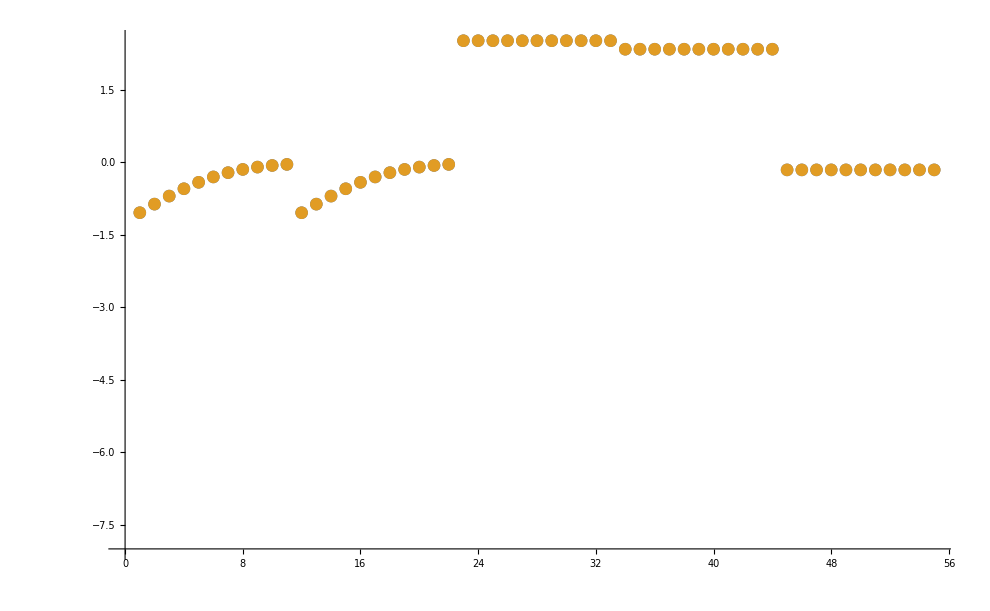

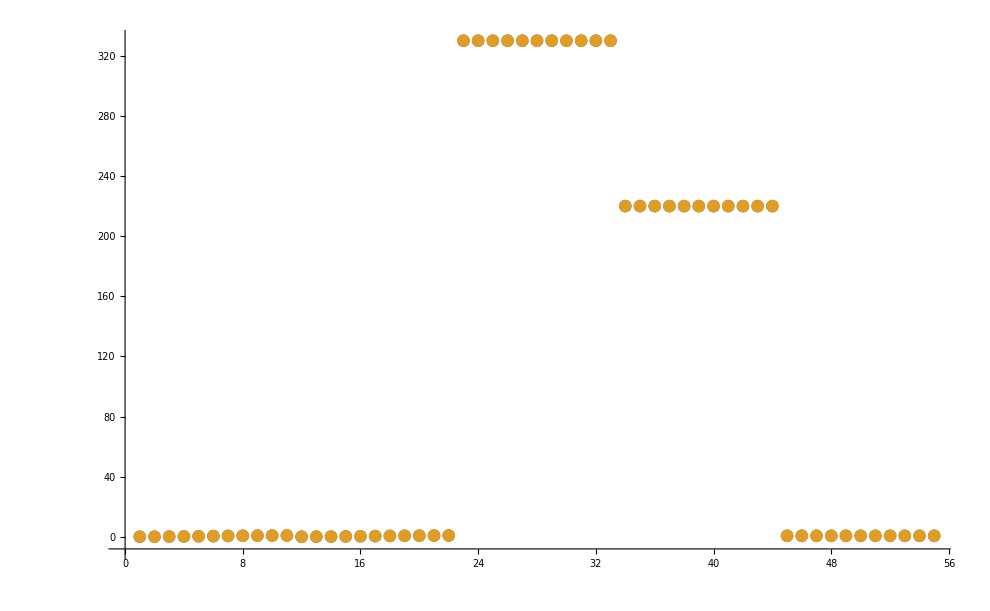

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

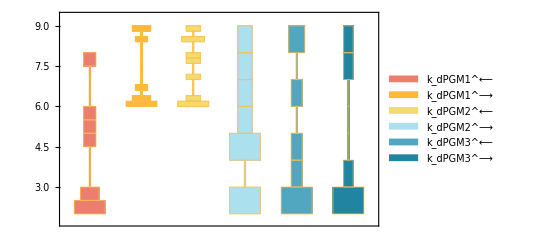

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

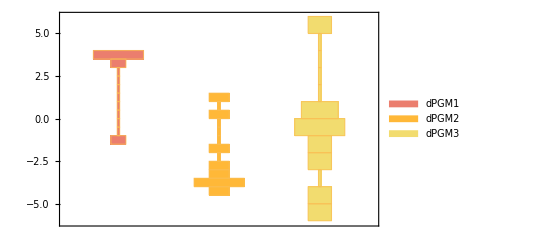

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

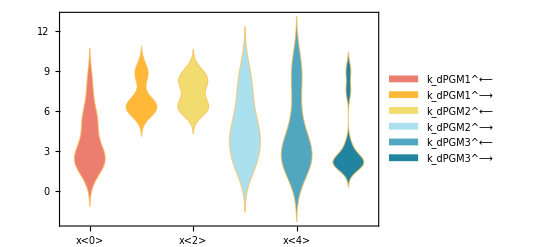

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[inputPath  <> "(.*)\\.txt"]->"$1"][[1]],{func,fittingData[[All,-2]]}];
```

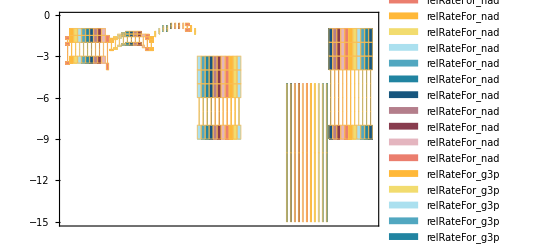

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> eTotal;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
(*Backcalculated Kms*)
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, KeqName]//TableForm
```

data value | predicted value | error in %
0.0002 | 0.00019985 | 0.0749771
0.00019 | 0.000190143 | 0.0751309

```mathematica
(*Backcalculated kcats*)
```

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
330 | 330. | 2.33312×10^-8
220 | 220. | 5.08482×10^-8

```mathematica
(*Backcalculated Haldane*)
```

```mathematica
backCalculateRatios[haldaneRatio,KeqEquilibrator,paramFitSub]//TableForm
```

data value | predicted value | error in %
0.7 | 0.700035 | 0.00498885